# :d83d:dce1 Bset 2: More Frequency Domain, LTI Systems

```mathematica
SetDirectory@NotebookDirectory[];
<<"../MMA library.m"
```

## 1. Moving Average

```mathematica
With[{context="movingaverage`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

```mathematica
fs=Import["hallelujah.wav","SampleRate"]
data=Import["hallelujah.wav","Data"][[2]];
Dimensions@data
```

44100

{791320}

```mathematica
movingAverage[data_]:=1/3 (RotateLeft[data]+data+RotateRight@data)
```

```mathematica
averaged=movingaverage`movingAverage@data;
```

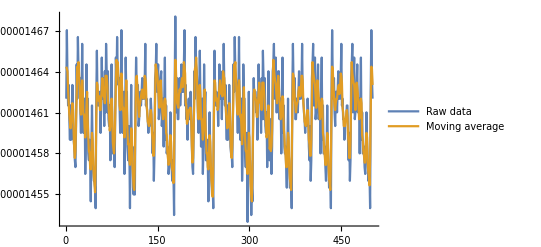

```mathematica
ListLinePlot[{data[[10000;;10500]],averaged[[10000;;10500]]},PlotLegends->{"Raw data","Moving average"},ImageSize->Full]
```

```mathematica
plotFFT@data
plotFFT@averaged
```

-Graphics-

-Graphics-

```mathematica
playSound[data,fs]
```

```mathematica
playSound[movingAverage@data,fs]
```

```mathematica
data[[1000;;1010]]
```

{2.69363×10^-6,3.59824×10^-6,-1.83955×10^-6,-8.657×10^-6,-6.34746×10^-6,-1.00569×10^-6,-5.12951×10^-6,-0.0000120531,-9.59699×10^-6,-4.31587×10^-6,-5.98864×10^-6}

```mathematica
With[{context="movingaverage`"},If[Context[]==context,End[],"Not in context"]]
```

movingaverage`

## 2. Remove Disturbances

```mathematica
With[{context="p2`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

```mathematica
fs=Import["provided files/Disturbance261.wav","SampleRate"]
x275=Import["provided files/Disturbance275.wav","Data"];
x275freq = 275.6181;
x261=Import["provided files/Disturbance261.wav","Data"];
x261freq=261.626;
xOrig=Import["provided files/DisturbanceOrig.wav","Data"];
```

22050

```mathematica
playSound[x261,fs]
```

```mathematica
playSound[x275,fs]
```

```mathematica
playSound[xOrig,fs]
```

```mathematica
plotFFT[x261]
```

-Graphics-

```mathematica
plotFFT@x275
```

-Graphics-

```mathematica
plotFFT@xOrig
```

-Graphics-

### Remove noise from 275hz signal: naive approach

```mathematica
(N@Ordering[Fourier@x275,-1][[1]]-1)*(2 Pi/Length@x275)*fs/(2 Pi)
```

275.618

```mathematica
fft=Fourier@x275;
```

Replace the top two magnitudes with zero

```mathematica
fft[[Ordering[fft,-2]]]=0;
```

Rebuild sound

```mathematica
sound=InverseFourier@fft;
```

```mathematica
plotFFT@sound
```

-Graphics-

Compare the results

```mathematica
playSound[Re@x275,fs]
```

```mathematica
playSound[Re@sound,fs]
```

```mathematica
With[{context="p2`"},If[Context[]==context,End[],"Not in context"]]
```

Not in context

### Remove 275hz noise: notch filter

notchFilter removes frequencies near freq (specified in radians per sample) with aggressiveness q (range 0-1)

```mathematica
notchFilter[data_,freq_,q_]:=
Module[{a,b,p,qq,r,y},
a=2q Cos@freq;
b=-q^2;
p=1;
qq=-2Cos@freq;
r=1;
y=ConstantArray[0,Length@data];
Do[
y[[n]]=a y[[n-1]]+b y[[n-2]]+p data[[n]]+qq data[[n-1]]+r data[[n-2]],
{n,3,Length@data}];
y
]
```

Pass the x275 through a notch filter

```mathematica
freq=x275freq*2 Pi /fs
```

0.0785379

```mathematica
filtered=notchFilter[x275,freq,.999];
```

```mathematica
plotFFT@filtered
```

-Graphics-

```mathematica
playSound[filtered,fs]
```

```mathematica
playSound[xOrig,fs]
```

### Remove noise from 261hz signal: naive approach

```mathematica
(N@Ordering[Fourier@x261,-1][[1]]-1)*(2 Pi/Length@x261)*fs/(2 Pi)
```

261.837

```mathematica
fft=Fourier@x261;
```

Replace the top bunch of magnitudes with zero

```mathematica
fft[[Ordering[Abs@fft,-30]]]=0;
```

Rebuild sound

```mathematica
sound=InverseFourier@fft;
```

```mathematica
plotFFT@sound
```

-Graphics-

Compare the results

```mathematica
playSound[Re@x261,fs]
```

```mathematica
playSound[Re@sound,fs]
```

```mathematica
playSound[Re@xOrig,fs]
```

```mathematica
With[{context="p2`"},If[Context[]==context,End[],"Not in context"]]
```

p2`

### Remove 261hz noise: notch filter

Pass the x275 through a notch filter

```mathematica
freq=x261freq*2 Pi /fs
```

0.0745508

```mathematica
filtered=notchFilter[x261,freq,.999];
```

```mathematica
plotFFT@filtered
```

-Graphics-

```mathematica
playSound[filtered,fs]
```

```mathematica
playSound[xOrig,fs]
```

```mathematica
With[{context="p2`"},If[Context[]==context,End[],"Not in context"]]
```

## 3. CTFT

```mathematica
With[{context="p3`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

```mathematica
Integrate[Exp[-t(I ω+1/τ)],{t,0,Infinity},Assumptions->{τ>0,ω>0}]
```

(ⅈ τ)/(ⅈ-τ ω)

```mathematica
With[{context="p3`"},If[Context[]==context,End[],"Not in context"]]
```

p3`

## 8.Circuits

```mathematica
With[{context="p8`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

```mathematica
RC=10^-3;
```

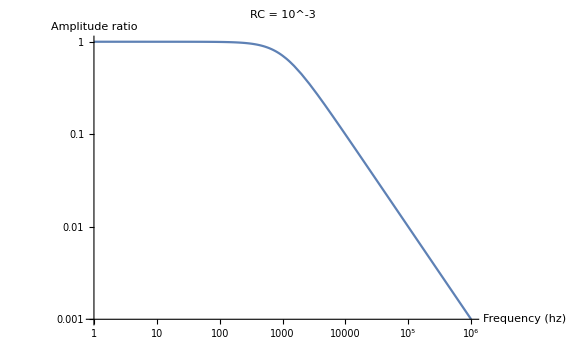

```mathematica
LogLogPlot[Abs[1/(1+RC I ω)],{ω,1,10^6},AxesLabel->{"Frequency (hz)","Amplitude ratio"},ImageSize->Large,PlotLabel->"RC = 10^-3"]
```

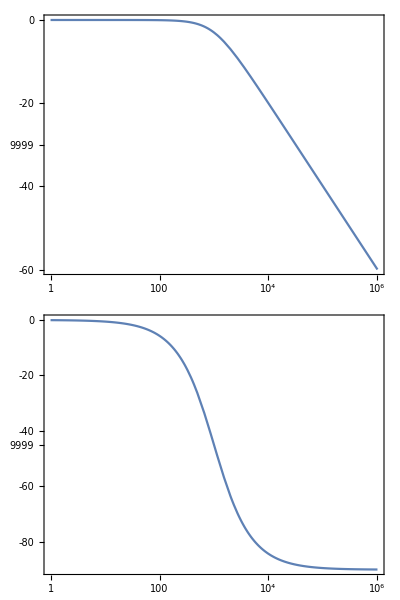

```mathematica
BodePlot[1/(1+RC I ω),{ω,1,10^6},ImageSize->Large]
```

```mathematica
With[{context="p8`"},If[Context[]==context,End[],"Not in context"]]
```

p8`

## Scratch work

```mathematica
exportNotebookPDF[]
```

/home/eric/Documents/School/QEA2/Acoustic Modem/Bset 2/Mathematica scratch.pdf

```mathematica
NotebookInformation[]
```

{FileName→FrontEnd`FileName[{$RootDirectory,home,eric,Documents,School,QEA2,Acoustic Modem,Bset 2},Mathematica scratch.nb,CharacterEncoding→UTF-8],FileModificationTime→3.68271×10^9,WindowTitle→Mathematica scratch.nb,MemoryModificationTime→3.68271×10^9,ModifiedInMemory→True,StorageSystem→Local,DocumentType→Notebook,MIMEType→application/vnd.wolfram.nb,StyleDefinitions→{FrontEndObject[LinkObject["c8gdu_shm", 3, 1]]4}}

```mathematica
NotebookDirectory[]
```

/home/eric/Documents/School/QEA2/Acoustic Modem/Bset 2/

```mathematica
ExpandFileName["/home/eric/Documents/School/QEA2/Acoustic Modem/Bset 2/"]
```

/home/eric/Documents/School/QEA2/Acoustic Modem/Bset 2/

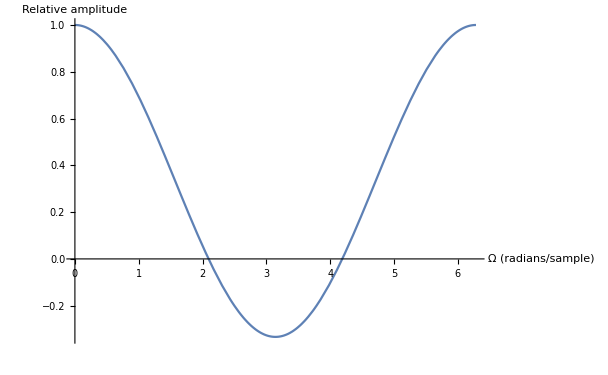

```mathematica
Plot[1/3(2 Cos@sig+1),{sig,0,2Pi},AxesLabel->{"Ω (radians/sample)","Relative amplitude"}]
```

```mathematica
StringReplace["/tmp/soundrand.wav","rand"-> ToString@RandomInteger[999]]
```

/tmp/sound203.wav

```mathematica
RandomInteger[999]
```

155